# AntonAntonov/MermaidJS

Graphics and images corresponding to mermaid-js specifications

## Paclet Manifest

"Documentation"

"Diagrams"

"MermaidJS-Animals-class-diagram.png"DocumentationDiagramsMermaidJS-Animals-class-diagram.png

"English"

"Guides"

"MakingMermaid-JSdiagrams.nb"DocumentationEnglishGuidesMakingMermaid-JSdiagrams.nb

"ReferencePages"

"Symbols"

"MermaidInk.nb"DocumentationEnglishReferencePagesSymbolsMermaidInk.nb

"MermaidJS.nb"DocumentationEnglishReferencePagesSymbolsMermaidJS.nb

"Tutorials"

"Kernel"

"MermaidJS.wl"KernelMermaidJS.wl

"LICENSE"LICENSE

"PacletInfo.wl"PacletInfo.wl

"README.md"README.md

"ResourceDefinition.nb"ResourceDefinition.nb

## Web Content

### Headline Image

### Basic Description

Functions to get graphics and images corresponding to a mermaid-js specifications via mermaid.ink or via mermaid-js' command line interface mermaid-cli.

### Details

Mermaid lets you create diagrams and visualizations using text and code.

Mermaid has different types of diagrams: Flowchart, Sequence Diagram, Class Diagram, State Diagram, Entity Relationship Diagram, User Journey, Gantt, Pie Chart, Requirement Diagram, and others.

Mermaid-js is a JavaScript based diagramming and charting tool that renders Markdown-inspired text definitions to create and modify diagrams dynamically.

MermaidJS and MermaidInk are very similar; the main difference is in which environment the mermaid-js specifications are converted into images.

MermaidInk uses the Web API mermaid.ink.

MermaidJS uses a local installation of mermaid-cli via the shell program mmdc.

### Primary Context

MyPublisherID`MyPaclet`

### Main Guide Page

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
```

```mathematica
Needs["AntonAntonov`MermaidJS`"];
```

### Basic Examples

Generate a flowchart from a Mermaid specification:

```mathematica
MermaidInk["
graph TD
    WL --> |ZMQ|Python --> |ZMQ|WL
"]
```

-Graphics-

Create a Graphics expression from a class diagram:

```mathematica
MermaidInk["
classDiagram
    Animal <|-- Duck
    Animal <|-- Fish
    Animal <|-- Zebra
    Animal : +int age
    Animal : +String gender
    Animal: +isMammal()
    Animal: +mate()
    class Duck{
        +String beakColor
        +swim()
        +quack()
    }
    class Fish{
        -int sizeInFeet
        -canEat()
    }
    class Zebra{
        +bool is_wild
        +run()
    }
"]
```

-Graphics-

### Scope

Here is class diagram that is a Graphics expression:

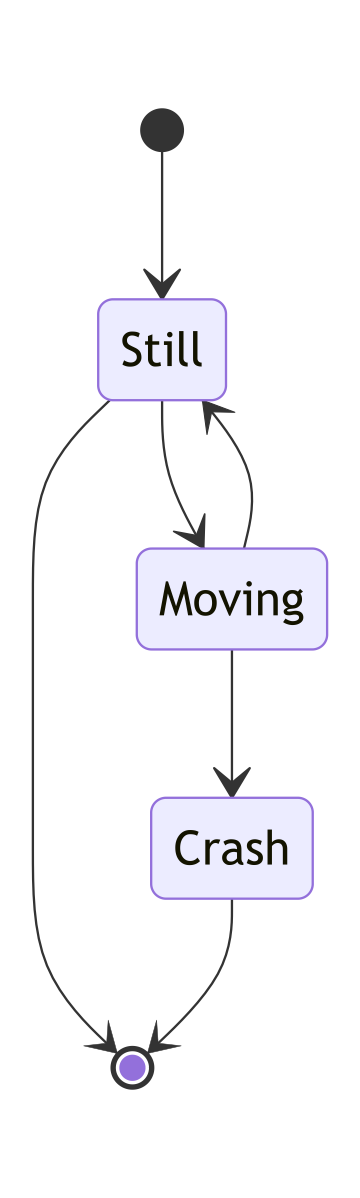

```mathematica
MermaidJS["
stateDiagram-v2
    [*] --> Still
    Still --> [*]

    Still --> Moving
    Moving --> Still
    Moving --> Crash
    Crash --> [*]
","PDF",ImageSize->Medium]
```

Here is the head of the expression above:

```mathematica
%//Head
```

Graphics

Additional options can be passed to mmdc with the third argument of MermaidJS. For example, if the PNG images are with too low resolution then the mmdc"--scale" option can be used:

```mathematica
MermaidJS["
graph LR
    WL --> |ZMQ|Python --> |ZMQ|WL
","PNG","MermaidOptions"->"--scale 2"]
```

-Graphics-

The first argument can be a Graph object -- the corresponding mermaid-js graph is produced. Here is a random graph that has both directed and undirected edges (some edges have tags):

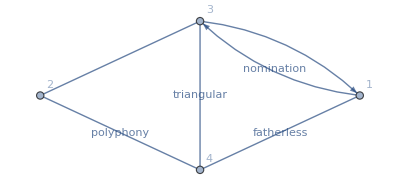

```mathematica
SeedRandom[45];
gr=GraphUnion[RandomGraph[{3,2},DirectedEdges->True],RandomGraph[{4,4},DirectedEdges->False]];
gr=Graph[Map[RandomChoice[{#,Append[#,RandomWord[]]}]&,EdgeList[gr]],VertexLabels->"Name",EdgeLabels->"EdgeTag"];
gr
```

Here is the corresponding mermaid-js image:

```mathematica
MermaidJS[gr]
```

-Graphics-

Here is a left-to-right version:

```mathematica
MermaidJS[gr,"MermaidDirectives"->"LR"]
```

-Graphics-

Very often Large Language Models (LLMs) produce Mermaid-JS code as a Markdown fenced code block. By default the fences are removed. Here we synthesize a Mermaid-JS specification:

```mathematica
spec=LLMSynthesize[{"Give a concise Mermaid-JS diagram of continents' land connections.",LLMPrompt["NothingElse"]["Mermaid-JS"]}]
```

```mermaid
graph LR
    NA(North America) --- SA(South America)
    NA --- EU(Europe)
    NA --- AF(Africa)
    EU --- AF
    EU --- AS(Asia)
    AF --- AS
    AS --- OC(Oceania)
```

Here we generate the corresponding diagram:

```mathematica
MermaidJS[spec]
```

-Graphics-

## Source & Additional Information

### Creator

Anton Antonov

### Source Control Repository

https://github.com/antononcube/WL-MermaidJS-paclet

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

Diagram

Mermaid

Graph

Class diagram

Sequence diagram

Flow chart

User journey

Entity Relationship Diagram

Pie chart

Gantt chart

UML

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

MermaidInk

### Original Source References and Attributions

Source, reference or citation

### Links

Link to other related material

### Compatibility

#### Wolfram Language Version

12.0+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

Wolfram Language system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

Wolfram Language built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

Paclet dependenciesDisclosuresPacletDependenciesChoose this option if your paclet directly installs or updates any additional paclets. Paclets that are included with the Wolfram system do not require a disclosure.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

Additional information about limitations, issues, etc.